```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
mub={0,100,200,300,400,500,550};
(*chi0=Table[Flatten[Import["./mub"<>ToString[mub[[i]]]<>"/data/V26.dat"]],{i,1,Length[mub]}];*)
chi0=Table[Flatten[Import["./mub"<>ToString[mub[[i]]]<>"/data/chi0.dat"]],{i,1,Length[mub]}];
T=Table[i,{i,21,300}];
pdata=Table[Transpose[{T,chi0[[i]]}],{i,1,Length[mub]}];
chi0data=Table[Transpose[{T,chi0[[i]]}],{i,1,Length[mub]}];
```

```mathematica
pint=Table[Interpolation[chi0data[[i]]],{i,1,Length[mub]}];
sint=Table[D[pint[[i]][x],x][[0]][x],{i,1,Length[mub]}];
sdata=Table[sint[[i]](*(sint[[i]]/x^3)/(chi1[[i]][[x]])*),{i,1,Length[mub]},{x,21,300}];
```

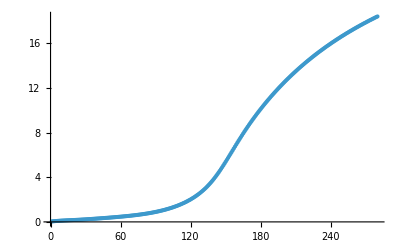

```mathematica
ListPlot[sdata[[1]]/T^3]
```

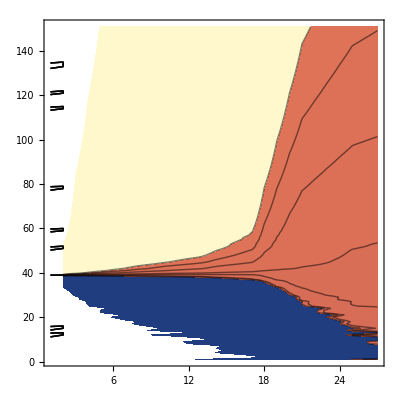

```mathematica
ListContourPlot[Transpose[sdata],Contours->{0.1,1,5,10,20,30,40}]
```